```mathematica
Clear["Global`*"]
```

## Skull model

Model 5: include collagen as a separate field

## Initialization

#### Load previous data

```mathematica
(*LoadFolder=OutNameRoot;*)
(*LoadFolder = "/Users/dang/Documents/Projects/Tabler_skull/Scripts/Scripts_mathematica/Plots_model4b_FD_solver/simulation3/200x100/data";*)
LoadFolder = "/Users/dang/Documents/Projects/Tabler_skull/Scripts/Scripts_mathematica/Plots_model4b_FD_solver/data";
LoadFolder = "/Users/dang/Documents/Projects/Tabler_skull/Scripts/Scripts_mathematica/Plots_model4b_FD_solver/simulation_set3/sim4b/data";
ρAll=Import[StringJoin[LoadFolder, "_rho_1.csv"]];
ϕAll=Import[StringJoin[LoadFolder, "_phi_1.csv"]];
VAll=Import[StringJoin[LoadFolder, "_V_1.csv"]];
```

```mathematica
Dimensions@VAll
```

{201,101}

```mathematica
Import[StringJoin[LoadFolder, "_parameters.csv"]]
```

{{eO,1000},{eM,30},{η,25/9},{ξ,2/9},{τ,10},{D1,15},{α,1/100000},{ρdA,0.0058},{ρdB,0.0076},{ρh,1/1000},{aρ,4},{a,4},{L,1500},{tmax,8},{Nx,200},{T,100}}

```mathematica
params={eO-> 1000, eM-> 30, η-> 25/9, ξ-> 5/18, τ-> 10, D1->1000, α-> 1/1000, ρdA-> 5.8*10^(-3), ρdB->7.6*10^(-3), ρh->1*10^(-3), aρ-> 8,a->8}; 
L=1500;
tmax=8;
Nx = 200;
T=100;
```

```mathematica
(* Define mesh *)
ΔxSet = 2L/(Nx);
ΔtSet = tmax/T;
xmesh= Range[-L, L, ΔxSet];
tmesh =Range[0, tmax, tmax/T];
```

## Exploring different models

### Examine choices for k_D

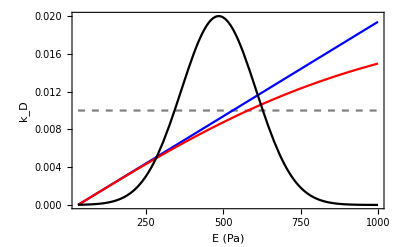

```mathematica
(*
kD := α (e-eM);
kD := Tanh[e];
*)
ϕ0[x_]:=(1-Tanh[a x/L])/2
e:= (eM(1-ϕ0[x])+eO ϕ0[x]);
params={eO-> 1000, eM-> 30, η-> 25/9, ξ-> 5/18, τ-> 10, D1->15, α-> 2*10^(-5), ρdA-> 5.8*10^(-3), ρdB->7.6*10^(-3),aρ->10,a->10,ρh->5*10^(-3)};
L=1500;

kD0:=0.01;
kD1:=α (e-eM);
kD2:=α eO  Tanh[(e-eM)/eO] /. params;
kD3:=0.02*Exp[-(e-(eO-eM)/2)^2/(2*(1/4(eO-eM)/2)^2)]
kD:=kD3

p0=Plot[{kD0/. params} , {e, eM/.params, (eO/.params)}, PlotStyle->{Gray, Dashed}];
p1=Plot[{kD1/. params} , {e, eM/.params, (eO/.params)}, PlotStyle->Blue];
p2=Plot[{kD2/. params} , {e, eM/.params, (eO/.params)}, PlotStyle->Red];
p3=Plot[{kD3/. params} , {e, eM/.params, (eO/.params)}, PlotStyle->Black];
Show[{p0,p1,p2,p3}, Frame-> True, FrameLabel-> {"E (Pa)", "k_D"}]
(*Plot[{kD3/. params} , {e, eM/.params, (eO/.params)}, PlotRange->All]*)
```

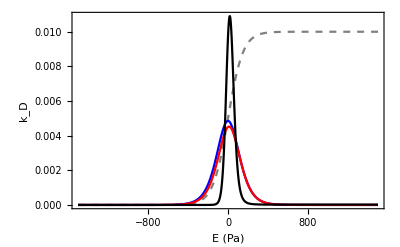

```mathematica
p0=Plot[{kD0(1-ϕ0[x])/. params} , {x, -L, L}, PlotStyle->{Gray, Dashed}, PlotRange->All];
p1=Plot[{kD1(1-ϕ0[x])/. params} , {x, -L, L}, PlotStyle->{Blue}, PlotRange->All];
p2=Plot[{kD2(1-ϕ0[x])/. params} , {x, -L, L}, PlotStyle->{Red}, PlotRange->All];
p3=Plot[{kD3(1-ϕ0[x])/. params} , {x, -L, L}, PlotStyle->{Black}, PlotRange->All];
Show[{p0,p1,p2,p3}, Frame-> True, FrameLabel-> {"E (Pa)", "k_D"}]
```

Differentiation rate

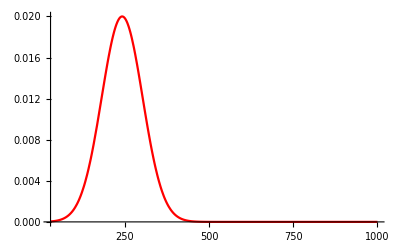

```mathematica
kD3b:=0.02*Exp[-(e-(eO-eM)/4)^2/(2*(1/4(eO-eM)/4)^2)] 
p3b=Plot[{kD3b/. params} , {e, eM/.params, (eO/.params)}, PlotStyle-> Red]
```

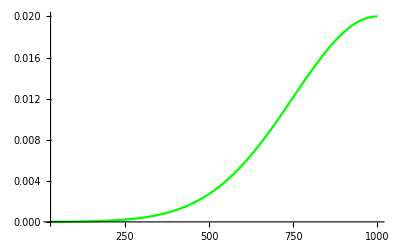

```mathematica
kD3c:=0.02*Exp[-(e-eO)^2/(2*(1/4 eO)^2)]
p3c=Plot[{kD3c/. params} , {e, eM/.params, (eO/.params)}, PlotStyle-> Green]
```

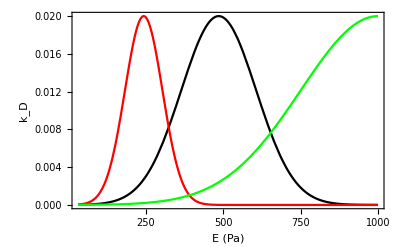

```mathematica
p3=Plot[{kD3/. params} , {e, eM/.params, (eO/.params)}, PlotStyle-> Black];
Show[{p3, p3b, p3c}, Frame-> True, FrameLabel-> {"E (Pa)", "k_D"}]
```

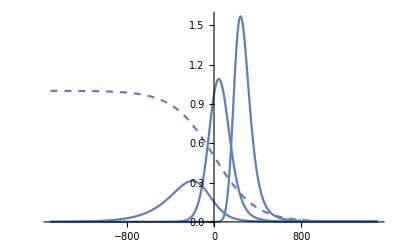

```mathematica
ϕ0[x_]:=(1-Tanh[a x/L])/2
e:=(eM(1-ϕ0[x])+eO ϕ0[x]) 
L=1500;
params={eO-> 1000, eM-> 30, η-> 25/9, ξ-> 5/18, τ-> 10, D1->15, α-> 2*10^(-5), ρdA-> 5.8*10^(-3), ρdB->7.6*10^(-3),aρ->4,a->4,ρh->5*10^(-3)};
pϕ=Plot[(ϕ0[x]) /.params, {x,-L,L}, PlotRange->All, PlotStyle->Dashed];
pDiff=Plot[100*(kD3*(1-ϕ0[x])) /.params, {x,-L,L}, PlotRange->All];
pDiffb=Plot[100*(kD3b*(1-ϕ0[x])) /.params, {x,-L,L}, PlotRange->All];
pDiffc=Plot[100*(kD3c*(1-ϕ0[x])) /.params, {x,-L,L}, PlotRange->All];
Show[pϕ, pDiff, pDiffb,pDiffc]
```

We can shift the differentiation peak by shifting the peak in the kD(E) profile. 
Moreover, the amplitude of the peak decreases towards the left, because the differentiation rate scales with (1-ϕ).

#### Predicted wave velocities

Wave velocity of general Fisher-KPP equation is 2 √D f'(0). For our system with f(ϕ) =k_D(1-ϕ), we get a velocity term 2√D (k_D'(ϕ)-k_D).

```mathematica
(*Simplify[(D[kD0, ϕ[x,t]]-kD0 )/.{ϕ[x,t]-> 0}], no Fisher wave since f[ϕ=0]≠0 *)
c1=Simplify[(D[kD1, ϕ[x,t]]-kD1 )/.{ϕ[x,t]-> 0}]
c2=Simplify[(D[kD2, ϕ[x,t]]-kD2 )/.{ϕ[x,t]-> 0}]
c3=Simplify[(D[kD3, ϕ[x,t]]-kD3 )/.{ϕ[x,t]-> 0}]
c1/.{ρ[x,t]-> ρh}
c2/.{ρ[x,t]-> ρh}
c3/.{ρ[x,t]-> ρh}
```

α (eM+((-2 eM+eO) ρ[x,t])/ρh)

1/50 (Tanh[3/100-6 ρ[x,t]]+194 Sech[3/100-6 ρ[x,t]]^2 ρ[x,t])

(ⅇ^(-(8 ((eM-eO) ρh+2 eM ρ[x,t])^2)/((eM-eO)^2 ρh^2)) ((-0.02 eM+0.02 eO) ρh^2+(0.64 eM ρh-0.64 eO ρh) ρ[x,t]+1.28 eM ρ[x,t]^2))/((eM-1. eO) ρh^2)

(-eM+eO) α

1/50 (194 ρh Sech[3/100-6 ρh]^2+Tanh[3/100-6 ρh])

(ⅇ^(-(8 (2 eM ρh+(eM-eO) ρh)^2)/((eM-eO)^2 ρh^2)) (1.28 eM ρh^2+(-0.02 eM+0.02 eO) ρh^2+ρh (0.64 eM ρh-0.64 eO ρh)))/((eM-1. eO) ρh^2)

```mathematica
N[2Sqrt[D1 c1]/.{ρ[x,t]-> ρh}/. params]
N[2Sqrt[D1 c2]/.{ρ[x,t]-> ρh}/. params]
N[2Sqrt[D1 c3]/.{ρ[x,t]-> ρh}/. params]
```

1.07889

1.07889

0.174593

Low values show that with our parameters the differentiation term doesn’t contribute much to wave propagation?!

#### Examine choices for ϕ_0[x]

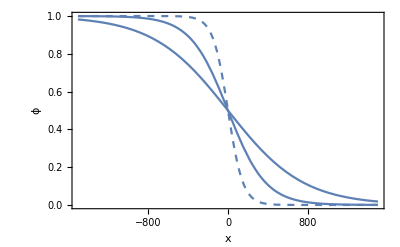

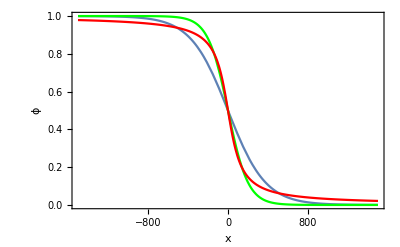

```mathematica
p1=Plot[{(1-Tanh[a x/L])/2} /. {a->4}, {x,-L,L}, Frame-> True, FrameLabel->{"x", "ϕ"}];
p1b=Plot[{(1-Tanh[a x/L])/2} /. {a->10}, {x,-L,L}, PlotStyle->Dashed, Frame-> True, FrameLabel->{"x", "ϕ"}];
p1c=Plot[{(1-Tanh[a x/L])/2} /. {a->2}, {x,-L,L}, Frame-> True, FrameLabel->{"x", "ϕ"}];

p2=Plot[(Exp[-α x]/(1+Exp[-α x])) /.{α-> 0.01}, {x,-L,L},PlotStyle->Green,Frame-> True,FrameLabel->{"x", "ϕ"}];
p3=Plot[(1-2/π ArcTan[α x])/2 /.{α->0.01}, {x,-L,L},PlotStyle->Red,Frame-> True,FrameLabel->{"x", "ϕ"}];
(*p2=Plot[(α/((2(x+L))^nh+c^nh)) /. {α-> 0.9*10^6,c-> 1000,nh-> 2},       {x, -L, L},PlotStyle->Red,Frame-> True,FrameLabel->{"x", "ϕ"}];*)
Show[{p1, p1b, p1c}]
Show[{p1,p2, p3}]
```

## Simulate model

### Parameters

These are parameters that gave nice looking solutions with NDSolve but aren’t necessarily relevant.

Important: it seems that we need ρ_h > ρ_A, ρ_B to get reasonable results for the velocity, because we need P>0 everywhere. 
It seems like only D = 1000 microns^2/hr gives reasonable results. For D > 1000 microns^2/hr the system becomes unsolvable.
Viscosity η does not seem to matter at all.
Friction γ sets the overall magnitude of the velocity.

```mathematica
(*Random parameters *)
(*params={ρdA->1, ρdB->1, τ-> 1, D1->.1, η->1, ξ->1, kF->0, z->1, α->1, eM->0.5,eO->1}; *)
(*
params={ρdA->1.1, ρdB->1.1, ρh-> 1.2, τ->0.1, D1->0.01, η->0.1, ξ->0.1, z->1, α->2, eM->0.1, eO->5, a->8}; 
(*params={eM->0.1, eO->1,η->0.1, ξ->0.1,τ->0.1, D1->0.01,  α->2,  ρdA->1.1, ρdB->1.1, ρh-> 1.2 };*)
L=1;
tmax=1;
(*Saved biological parameters*)
(*params={eO-> 1000, eM-> 30, η-> 25/9, ξ-> 5/18, τ-> 12, D1->3600, α-> 1/1000, ρdA-> 10^(-2), ρdB-> 10^(-2), ρh->1.2*10^(-2), a->8};  (* higher a = steeper Tanh function *)*)
params={eO-> 1000, eM-> 30, η-> 25/9, ξ-> 5/18, τ-> 10, D1->1000, α-> 10^(-4)/4, ρdA-> 5.8*10^(-3), ρdB->7.6*10^(-3), ρh->1*10^(-3), aρ-> 6,a->6}; 
L=1500;
tmax=8;
*)
```

```mathematica
(* to play around with *)
(*params={eO-> 1000, eM-> 30, η-> 25/9, ξ-> 3/18, τ-> 10, D1->1000, α-> 2*10^(-5), ρdA-> 5.8*10^(-3), ρdB->7.6*10^(-3), ρh->1*10^(-3), aρ->4,a->4}; 
L=1500;
tmax=8;
*)
(*time in s, length in mm*) 
(*
params = {eO-> 1000, eM-> 30, η-> 10^4, ξ-> 10^9, τ-> 3600, D1-> 10^(-6), α-> 36, ρdA-> 10^4, ρdB-> 10^4}; 
L=1;
tmax=1000;
*)
(*time in hr, length in μm*)
(*params={eO-> 1000, eM-> 30, η-> 25/9, ξ-> 5/18, τ-> 12, D1->3600, α-> 1/1000, ρdA-> 10^(-2), ρdB-> 10^(-2), ρh->1.2*10^(-2), a->8};  (* higher a = steeper Tanh function *)*)
(*params={eO-> 1000, eM-> 30, η-> 25/9, ξ-> 5/18, τ-> 10, D1->3600, α-> 1/100, ρdA-> 10^(-2), ρdB-> 10^(-2), ρh-> 1/2*10^(-2)};*)
(*params={eO-> 1000, eM-> 30, η-> 25/9, ξ-> 5/18, τ-> 1, D1->1, α-> 1/100, ρdA-> 10^(0), ρdB-> 10^(0), ρh-> 10^(0)};*)
(*L=500; (* consistent with input data!*)
tmax=6;
*)
```

```mathematica
(* === new value of D1~15 === *)
(* sim 4 *)
(*params={eO-> 1000, eM-> 30, η-> 25/9, ξ->5/18, τ->10, D1->15, α->1*10^(-5), ρdA->5.8*10^(-3), ρdB->7.6*10^(-3),aρ->4,a->4,ρh->1*10^(-3), f->0};*)
(* sim 4b *)
params={eO-> 1000, eM-> 30, η-> 25/9, ξ->2/9,τ->10,D1->15,α->1*10^(-5),ρdA->5.8*10^(-3),ρdB->7.6*10^(-3),aρ->8,a->8,ρh->1*10^(-3), f->0};

(* play around *)
(*params={eO-> 1000, eM-> 30, ηM-> 10^3/3600, ηO-> 10^5/3600, ξ->2/9,τ->10,D1->15,α->1*10^(-5),ρdA->5.8*10^(-3),ρdB->7.6*10^(-3),aρ->4,a->4,ρh->1*10^(-3), f->0, tc-> 10};*)
(*params={eO-> 1000, eM-> 30, η-> 25/9, ξ->0.28,τ->10,D1->15,α->1*10^(-5),ρdA->5.8*10^(-3),ρdB->7.6*10^(-3),aρ->2,a->4,ρh->1*10^(-3), f->0.28*0.1};*)
(*params={eO-> 1000, eM-> 30, η-> 25/9, ξ->0.28,τ->10,D1->15,α->1*10^(-5),ρdA->5.8*10^(-3),ρdB->7.6*10^(-3),aρ->2,a->6,ρh->1*10^(-3), f->0};*)

(*params={eO-> 1000, eM-> 30, η-> 25/9, ξ->5/18,τ->10,D1->15,α->2*10^(-5),ρdA->5.8*10^(-3),ρdB->7.6*10^(-3),aρ->4,a->4,ρh->5*10^(-3), f->0};*)
L=1500;
tmax=8;
```

#### Estimate some parameters

```mathematica
αEst =α1/.First@Solve[ vw==vc+Sqrt[ D1(α1 (eO-eM)+(kB-kA)/.{ρ[x,t]-> (ρdA+ρdB)/2}  )], α1] /. {vw-> 20, vc ->12 }/. params
```

0.00437042

```mathematica
(* proliferation term *)
D1(kB-kA)/.{ρ[x,t]-> (ρdA+ρdB)/2}/. params
(* stiffness term *)
N[D1(α1 (eO-eM)) /. params/.{α1-> 10^(-6)}]
```

0.41039

0.01455

```mathematica
(* Wave velocity term *)
Sqrt[D1(α1 (eO-eM))+ D1(kB-kA)/.{ρ[x,t]-> (ρdA+ρdB)/2} ] /. params/.{α1-> αEst}
```

8.

#### Initial conditions

```mathematica
ρ0[x_]:=(Tanh[aρ x/L]+1)/2 (ρdA-ρdB)+ ρdB;
ϕ0[x_]:=(1-Tanh[a x/L])/2;
c0[x_]:= eM+(eO-eM)( 1/2-x/(2L));
iv={ρ[x,0]==ρ0[x],ϕ[x,0]==ϕ0[x],v[x,0]==0} /. params;
(*iv={ρ[x,0]==ρ0[x],ϕ[x,0]==fData[x],v[x,0]==0} /. params;*)
bc={ρ[-L,t]==ρ0[-L],ρ[L,t]==ρ0[L],ϕ[-L,t]==ϕ0[-L],ϕ[L,t]==ϕ0[L],v[-L,t]==0,v[L,t]==0} /. params;
```

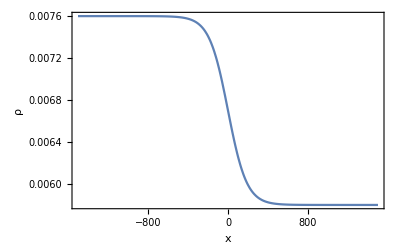
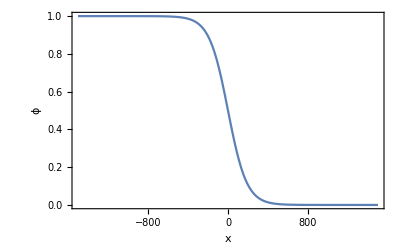
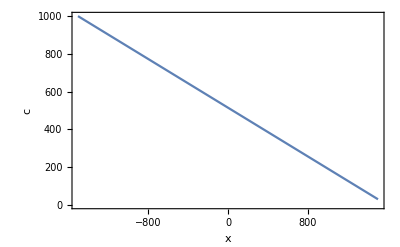

```mathematica
{Plot[{ρ0[x]} /. params, {x, -L, L}, Frame-> True, FrameLabel->{"x", "ρ"}], Plot[{ϕ0[x]} /. params, {x, -L, L}, Frame-> True, FrameLabel->{"x", "ϕ"}],
Plot[{c0[x]} /. params, {x, -L, L}, Frame-> True, FrameLabel->{"x", "c"}]}
```

#### PDE system

```mathematica
kA:=1/τ((ρdA-ρ[x,t])/ρdA);
kB:=1/τ((ρdB-ρ[x,t])/ρdB); 
(* Stiffness *)
(*e:= c[x,t]/d ;  *)
(*e:= (eM(1-ϕ[x,t])+eO ϕ[x,t]) (ρ[x,t]/ρh);*)
(*kD := α (e-eM); *)
```

```mathematica
(* Viscosity *)
Clear[η];
η:= (ηM(1-ϕ[x,t])+ηO ϕ[x,t]);
```

```mathematica
kD0:=0.01;
kD1:=α (e-eM);
kD2:=α eO  Tanh[(e-eM)/eO] /. params;
kD3:=0.02*Exp[-(e-(eO-eM)/2)^2/(2*((eO-eM)/8)^2)];
kD3b:=0.02*Exp[-(e-(eO-eM)/4)^2/(2*(1/4(eO-eM)/4)^2)];
kD3c:=0.02*Exp[-(e-eO)^2/(2*(1/4 eO)^2)];
kD:=kD1
```

```mathematica
PDEsys={D[ρ[x,t],t]+D[ρ[x,t] (v[x,t]),x]==(kA (1-ϕ[x,t])+kB ϕ[x,t]) ρ[x,t],D[ϕ[x,t],t]+(v[x,t]) D[ϕ[x,t],x]==D1 D[ϕ[x,t],{x,2}]+ D1 D[ρ[x,t],x] D[ϕ[x,t],x]/ρ[x,t]+(kB-kA) ϕ[x,t] (1-ϕ[x,t])+kD (1-ϕ[x,t]),
ρ[x,t](η D[v[x,t],{x,2}]-ξ v[x,t])==c[x,t] D[ρ[x,t],x] + D[c[x,t], x] Log[ρ[x,t]/ρh]*ρ[x,t] + f,
D[c[x,t],t]== tc ^(-1)( (eM + (eO-eM)ϕ[x,t])-c[x,t])};
vars={ρ,ϕ,v};
fullsys=Join[PDEsys/.params,bc,iv]
```

{ρ^(0,1)[x,t]+ρ[x,t] v^(1,0)[x,t]+v[x,t] ρ^(1,0)[x,t]==ρ[x,t] (17.2414 (0.0058-ρ[x,t]) (1-ϕ[x,t])+13.1579 (0.0076-ρ[x,t]) ϕ[x,t]),ϕ^(0,1)[x,t]+v[x,t] ϕ^(1,0)[x,t]==((-30+e) (1-ϕ[x,t]))/100000+(-17.2414 (0.0058-ρ[x,t])+13.1579 (0.0076-ρ[x,t])) (1-ϕ[x,t]) ϕ[x,t]+(15 ρ^(1,0)[x,t] ϕ^(1,0)[x,t])/ρ[x,t]+15 ϕ^(2,0)[x,t],ρ[x,t] (-2/9 v[x,t]+25/9 v^(2,0)[x,t])==Log[1000 ρ[x,t]] ρ[x,t] c^(1,0)[x,t]+c[x,t] ρ^(1,0)[x,t],c^(0,1)[x,t]==(30-c[x,t]+970 ϕ[x,t])/tc,ρ[-1500,t]==0.0076,ρ[1500,t]==0.0058,ϕ[-1500,t]==1/2 (1+Tanh[8]),ϕ[1500,t]==1/2 (1-Tanh[8]),v[-1500,t]==0,v[1500,t]==0,ρ[x,0]==0.0076-0.0009 (1+Tanh[(2 x)/375]),ϕ[x,0]==1/2 (1-Tanh[(2 x)/375]),v[x,0]==0}

#### NDSolve

```mathematica
ndsol=NDSolve[fullsys,vars,{x,-L,L},{t,0,tmax},Method->{"EquationSimplification"->"Residual","IndexReduction"->Automatic}]
(*, InterpolationOrder->All, PrecisionGoal-> Infinity, MaxStepSize->30] *)(*, MaxSteps->100000, MaxStepSize->1] *)
```

NDSolve::femnlmdor: The maximum derivative order of the nonlinear PDE coefficients for the Finite Element Method is larger than 1. It may help to rewrite the PDE in inactive form.

NDSolve[{ρ^(0,1)[x,t]+ρ[x,t] v^(1,0)[x,t]+v[x,t] ρ^(1,0)[x,t]==ρ[x,t] (17.2414 (0.0058-ρ[x,t]) (1-ϕ[x,t])+13.1579 (0.0076-ρ[x,t]) ϕ[x,t]),ϕ^(0,1)[x,t]+v[x,t] ϕ^(1,0)[x,t]==((-30+e) (1-ϕ[x,t]))/100000+(-17.2414 (0.0058-ρ[x,t])+13.1579 (0.0076-ρ[x,t])) (1-ϕ[x,t]) ϕ[x,t]+(15 ρ^(1,0)[x,t] ϕ^(1,0)[x,t])/ρ[x,t]+15 ϕ^(2,0)[x,t],ρ[x,t] (-2/9 v[x,t]+25/9 v^(2,0)[x,t])==Log[1000 ρ[x,t]] ρ[x,t] c^(1,0)[x,t]+c[x,t] ρ^(1,0)[x,t],c^(0,1)[x,t]==(30-c[x,t]+970 ϕ[x,t])/tc,ρ[-1500,t]==0.0076,ρ[1500,t]==0.0058,ϕ[-1500,t]==1/2 (1+Tanh[8]),ϕ[1500,t]==1/2 (1-Tanh[8]),v[-1500,t]==0,v[1500,t]==0,ρ[x,0]==0.0076-0.0009 (1+Tanh[(2 x)/375]),ϕ[x,0]==1/2 (1-Tanh[(2 x)/375]),v[x,0]==0},{ρ,ϕ,v},{x,-1500,1500},{t,0,8},Method→{EquationSimplification→Residual,IndexReduction→Automatic}]

```mathematica
{DensityPlot[ρ[x,t]/.ndsol[[1]],{x,-L,L},{t,0,tmax},Mesh->None,PlotRange-> All, AxesLabel->Automatic,PlotLegends->Automatic, PlotLabel->"ρ"],
DensityPlot[ϕ[x,t]/.ndsol[[1]],{x,-L,L},{t,0,tmax},Mesh->None,PlotRange-> All,AxesLabel->Automatic,PlotLegends->Automatic, PlotLabel->"ϕ"],
DensityPlot[v[x,t]/.ndsol[[1]],{x,-L,L},{t,0,tmax},Mesh->None,PlotRange-> All,AxesLabel->Automatic,PlotLegends->Automatic, PlotLabel->"v"]}
```

NDSolve::dsvar: -1499.79 cannot be used as a variable.

ReplaceAll::reps: {ρ^(0,1)[-1499.79,0.000571429]+ρ[-1499.79,0.000571429] v^(1,0)[-1499.79,0.000571429]+v[-1499.79,0.000571429] ρ^(1,0)[-1499.79,0.000571429]==ρ[-1499.79,0.000571429] («1»),«11»,v[-1499.79,0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {ρ^(0,1)[-1499.79,0.000571429]+ρ[-1499.79,0.000571429] v^(1,0)[-1499.79,0.000571429]+v[-1499.79,0.000571429] ρ^(1,0)[-1499.79,0.000571429]==ρ[-1499.79,0.000571429] («1»),«11»,v[-1499.79,0.]==0.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: -1285.5 cannot be used as a variable.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: -1071.21 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

{-Graphics-,-Graphics-,-Graphics-}

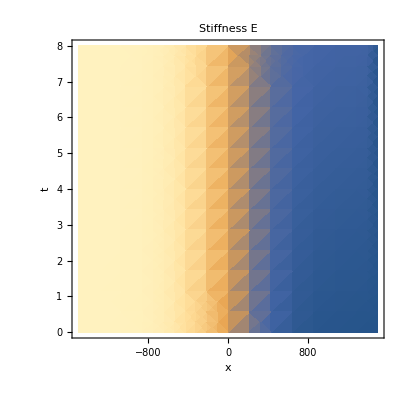

```mathematica
DensityPlot[(eM(1-ϕ[x,t])+eO ϕ[x,t])/. params/.ndsol[[1]],{x,-L,L},{t,0,tmax},Mesh->None,PlotRange-> All, AxesLabel->Automatic,PlotLabel->"Stiffness E"]
```

#### Discretized PDE system

```mathematica
(* Equations for PDE *)
(* Time derivative*)
discretizationT={Derivative[0,1][ρ][x,t]->  (Subscript[ρ, i,m+1]-Subscript[ρ, i,m])/Δt, Derivative[0,1][ϕ][x,t]->  (Subscript[ϕ, i,m+1]-Subscript[ϕ, i,m])/Δt, Derivative[0,1][c][x,t]->  (Subscript[c, i,m+1]-Subscript[c, i,m])/Δt}; (* forward scheme*)

(* 1. forward Euler schemes*)
(* a. explicit scheme, centered diff *)
discretization1 = 
{ρ[x,t]-> Subscript[ρ, i,m], Derivative[1,0][ρ][x,t]-> (Subscript[ρ, i+1,m]-Subscript[ρ, i-1,m])/(2 Δx), 
ϕ[x,t]-> Subscript[ϕ, i,m], Derivative[1,0][ϕ][x,t]-> (Subscript[ϕ, i+1,m]-Subscript[ϕ, i-1,m])/(2 Δx),Derivative[2,0][ϕ][x,t]-> (Subscript[ϕ, i+1,m]- 2 Subscript[ϕ, i,m] + Subscript[ϕ, i-1,m])/(Δx)^2,
v[x,t]-> Subscript[v, i,m], Derivative[1,0][v][x,t]-> (Subscript[v, i+1,m]-Subscript[v, i-1,m])/(2 Δx),Derivative[2,0][v][x,t]-> (Subscript[v, i+1,m]- 2 Subscript[v, i,m] + Subscript[v, i-1,m])/(Δx)^2, 
c[x,t]->Subscript[c, i,m], Derivative[1,0][c][x,t]-> (Subscript[c, i+1,m]-Subscript[c, i-1,m])/(2 Δx)};
pdeDiscretized1 =PDEsys /.discretizationT /. discretization1;

(* b. explicit scheme, fwd diff *)
(*discretization1b = {ϕ[x,t]-> Subscript[ϕ, i,m], ϕ^(0,1)[x,t]->  (Subscript[ϕ, i,m+1]-Subscript[ϕ, i,m])/Δt,ϕ^(1,0)[x,t]-> (Subscript[ϕ, i+1,m]-Subscript[ϕ, i,m])/(2 Δx),ϕ^(2,0)[x,t]-> (Subscript[ϕ, i+1,m]- 2 Subscript[ϕ, i,m] + Subscript[ϕ, i-1,m])/(Δx)^2,V[x,t]-> Subscript[V, i,m], V^(2,0)[x,t]-> (Subscript[V, i+1,m]- 2 Subscript[V, i,m] + Subscript[V, i-1,m])/(Δx)^2};  
pdeDiscretized =PDEsys /.discretizationT /. discretization1b;*) 

(* 2. backward Euler scheme *) 
(* implicit scheme, centered diff *)
(* NB cannot use implicit scheme for equation for V*)
discretization2 = Join[{ρ[x,t]-> Subscript[ρ, i,m], Derivative[1,0][ρ][x,t]-> (Subscript[ρ, i+1,m]-Subscript[ρ, i-1,m])/(2 Δx),ϕ[x,t]-> Subscript[ϕ, i,m], Derivative[1,0][ϕ][x,t]-> (Subscript[ϕ, i+1,m]-Subscript[ϕ, i-1,m])/(2 Δx),Derivative[2,0][ϕ][x,t]-> (Subscript[ϕ, i+1,m]- 2 Subscript[ϕ, i,m] + Subscript[ϕ, i-1,m])/(Δx)^2}/.{m->m+1}, {v[x,t]-> Subscript[v, i,m],Derivative[1,0][v][x,t]-> (Subscript[v, i+1,m]-Subscript[v, i-1,m])/(2 Δx), Derivative[2,0][v][x,t]-> (Subscript[v, i+1,m]- 2 Subscript[v, i,m] + Subscript[v, i-1,m])/(Δx)^2}];

pdeDiscretized2 =Join[ PDEsys[[;;2]]/.discretizationT /. discretization2, {PDEsys[[3]]/.discretizationT /. discretization1}];

(* 3. Crank-Nicolson scheme: combine discretizations *)
discretization3= {ρ[x,t]->( Subscript[ρ, i,m] + Subscript[ρ, i,m+1])/2, Derivative[1,0][ρ][x,t]-> ((Subscript[ρ, i+1,m]-Subscript[ρ, i-1,m])/(2 Δx)+(Subscript[ρ, i+1,m+1]-Subscript[ρ, i-1,m+1])/(2 Δx))/2,ϕ[x,t]-> (Subscript[ϕ, i,m]+Subscript[ϕ, i,m+1])/2, Derivative[1,0][ϕ][x,t]-> ((Subscript[ϕ, i+1,m]-Subscript[ϕ, i-1,m])/(2 Δx)+(Subscript[ϕ, i+1,m+1]-Subscript[ϕ, i-1,m+1])/(2 Δx))/2,Derivative[2,0][ϕ][x,t]-> ((Subscript[ϕ, i+1,m]- 2 Subscript[ϕ, i,m] + Subscript[ϕ, i-1,m])/(Δx)^2+(Subscript[ϕ, i+1,m+1]- 2 Subscript[ϕ, i,m+1] + Subscript[ϕ, i-1,m+1])/(Δx)^2)/2,
v[x,t]-> (Subscript[v, i,m]+Subscript[v, i,m+1])/2,Derivative[1,0][v][x,t]-> ((Subscript[v, i+1,m]-Subscript[v, i-1,m])/(2 Δx)+(Subscript[v, i+1,m]-Subscript[v, i-1,m])/(2 Δx))/2, Derivative[2,0][v][x,t]->( (Subscript[v, i+1,m]- 2 Subscript[v, i,m] + Subscript[v, i-1,m])/(Δx)^2+(Subscript[v, i+1,m+1]- 2 Subscript[v, i,m+1] + Subscript[v, i-1,m+1])/(Δx)^2)/2};
```

```mathematica
pdeDiscretized = pdeDiscretized1;
pdeDiscretized/.params
```

{((-v_(-1+i,m)+v_(1+i,m)) ρ_(i,m))/(2 Δx)+(-ρ_(i,m)+ρ_(i,1+m))/Δt+(v_(i,m) (-ρ_(-1+i,m)+ρ_(1+i,m)))/(2 Δx)==ρ_(i,m) (17.2414 (0.0058-ρ_(i,m)) (1-ϕ_(i,m))+13.1579 (0.0076-ρ_(i,m)) ϕ_(i,m)),(-ϕ_(i,m)+ϕ_(i,1+m))/Δt+(v_(i,m) (-ϕ_(-1+i,m)+ϕ_(1+i,m)))/(2 Δx)==(-17.2414 (0.0058-ρ_(i,m))+13.1579 (0.0076-ρ_(i,m))) (1-ϕ_(i,m)) ϕ_(i,m)+((1-ϕ_(i,m)) (-30+30 (1-ϕ_(i,m))+1000 ϕ_(i,m)))/100000+(15 (-ρ_(-1+i,m)+ρ_(1+i,m)) (-ϕ_(-1+i,m)+ϕ_(1+i,m)))/(4 Δx^2 ρ_(i,m))+(15 (ϕ_(-1+i,m)-2 ϕ_(i,m)+ϕ_(1+i,m)))/Δx^2,ρ_(i,m) (-(2 v_(i,m))/9+((v_(-1+i,m)-2 v_(i,m)+v_(1+i,m)) (5/18 (1-ϕ_(i,m))+(250 ϕ_(i,m))/9))/Δx^2)==(Log[1000 ρ_(i,m)] (-c_(-1+i,m)+c_(1+i,m)) ρ_(i,m))/(2 Δx)+(c_(i,m) (-ρ_(-1+i,m)+ρ_(1+i,m)))/(2 Δx),(-c_(i,m)+c_(i,1+m))/Δt==1/10 (30-c_(i,m)+970 ϕ_(i,m))}

### Solve discretized system: initialization

```mathematica
(* Define mesh *)
Nx=50;
T= 100;
ΔxSet = 2L/(Nx);
ΔtSet = tmax/T;
xmesh= Range[-L, L, ΔxSet];
tmesh =Range[0, tmax, tmax/T];
Print[xmesh[[Nx/2+1]]];
Print[ N@ΔxSet]
Print[ N@ΔtSet]
```

0

60.

0.08

```mathematica
(* Boundary conditions *)
ρL=ρ0[-L] /. params; ρR=ρ0[L] /. params; 
(*ϕL = 1; ϕR = 0;*)
ϕL = ϕ0[-L]/.params; ϕR = ϕ0[L]/.params;
VL = 0; VR = 0;
cL = c0[-L]/.params; cR =  c0[L]/.params;

bcρ={Subscript[ρ, 0,m]==ρL,Subscript[ρ, Nx,m]==ρR};
bcϕ={Subscript[ϕ, 0,m]==ϕL,Subscript[ϕ, Nx,m]==ϕR};
bcV={Subscript[v, 0,m]==VL,Subscript[v, Nx,m]==VR};
bcc={Subscript[c, 0,m]==cL,Subscript[c, Nx,m]==cR};
bcρRepl={Subscript[ρ, 0,m]-> ρL,Subscript[ρ, Nx,m]->ρR};
bcϕRepl={Subscript[ϕ, 0,m]-> ϕL,Subscript[ϕ, Nx,m]->ϕR};
bcVRepl={Subscript[v, 0,m]-> VL,Subscript[v, Nx,m]->VR};
bccRepl={Subscript[c, 0,m]-> cL,Subscript[c, Nx,m]->cR};

(* Initial conditions *)
ρ0Set=Table[ ρ0[ xmesh[[i]] ] /. params, {i,1,Nx+1}];
(*ϕ0Set=Table[Boole[(i<Nx/2)], {i, 0, Nx}];*)
ϕ0Set=Table[ ϕ0[xmesh[[i]]], {i,0, Nx}] /. params; 
c0Set=Table[ c0[xmesh[[i]]], {i,0, Nx}] /. params;
```

```mathematica
(* Initialize values *)
ρAll=Table[Subscript[ρ, i,m], {i, 0, Nx}, {m, 0, T}];
ϕAll=Table[Subscript[ϕ, i,m], {i, 0, Nx}, {m, 0, T}];
VAll=Table[Subscript[v, i,m], {i, 0, Nx}, {m, 0, T}];
cAll=Table[Subscript[c, i,m], {i, 0, Nx}, {m, 0, T}];

(* set initial values*)
Do[ρAll[[i+1, 1]] =ρ0Set[[i+1]], {i,0,Nx}]; 
Do[ϕAll[[i+1, 1]] =ϕ0Set[[i+1]], {i,0,Nx}]; 
Do[cAll[[i+1, 1]] =c0Set[[i+1]], {i,0,Nx}]; 

(* set Dirichlet boundary values *)
Do[ρAll[[1, j+1]] = ρL, {j, 0, T}]
Do[ρAll[[Nx+1, j+1]] = ρR, {j, 0, T}]
Do[ϕAll[[1, j+1]] = ϕL, {j, 0, T}]
Do[ϕAll[[Nx+1, j+1]] = ϕR, {j, 0, T}]
Do[VAll[[1, j+1]] = VL, {j, 0, T}]
Do[VAll[[Nx+1, j+1]] = VR, {j, 0, T}]
Do[cAll[[1, j+1]] = cL, {j, 0, T}]
Do[cAll[[Nx+1, j+1]] = cR, {j, 0, T}]
```

```mathematica
(* Only for Crank-Nicolson: initial values for V*)
(*
Vt0[x_]:=0;
Vt0Set=Table[Vt0[xmesh[[i]]], {i,0, Nx}] /. params;
Do[ VAll[[i+1, 1]] =Vt0Set[[i+1]], {i,0,Nx}];
*)
```

### Solve discretized system: explicit method

#### Test

```mathematica
thism = 0;

(* current values *)
ρReplace=MapThread[#1->#2&,{Table[Subscript[ρ, i,thism] , {i,0, Nx}], ρAll[[;;, thism+1]]}];
ϕReplace=MapThread[#1->#2&,{Table[Subscript[ϕ, i,thism] , {i,0, Nx}], ϕAll[[;;, thism+1]]}]; VReplace=MapThread[#1->#2&,{Table[Subscript[v, i,thism] , {i,0, Nx}], VAll[[;;, thism+1]]}];
cReplace=MapThread[#1->#2&,{Table[Subscript[c, i,thism] , {i,0, Nx}], cAll[[;;, thism+1]]}];

(* boundary conditions *)
bcJoined =Flatten@Table[Join[bcρRepl, bcϕRepl, bcVRepl, bccRepl], {m, thism, thism+1}];

(* def system *)
pdeTemp=(pdeDiscretized /. {m-> thism, Δx -> ΔxSet,Δt -> ΔtSet} /. params);
condsAll=Flatten@Table[pdeTemp/. bcJoined /.ρReplace/. ϕReplace /. VReplace /. cReplace  , {i, 1, Nx-1}];
varlist=Flatten@Table[{Subscript[ρ, i,m],Subscript[v, i,m], Subscript[ϕ, i,m], Subscript[c, i,m]}, {i,1,Nx-1}] /. {m->thism}; 

(* variables to solve*)
(* Solve for V*)
condsAll=Join[bcV/. {m-> thism},Table[pdeTemp[[3]] , {i, 1, Nx-1}]]/.ρReplace /.ϕReplace /.cReplace;
Vlist=Table[Subscript[v, i,m], {i,0,Nx}] /. {m-> thism};
VDiscNSol=First@NSolve[condsAll, Vlist];
VAll=(VAll/.VDiscNSol);
(* Solve for ρ, ϕ, c*)
If[thism<T,
condsAll=Join[bcρ/.{m->thism+1},bcϕ/.{m->thism+1},bcc/.{m->thism+1}, Table[pdeTemp[[1]] , {i, 1, Nx-1}], Table[pdeTemp[[2]] , {i, 1, Nx-1}], Table[pdeTemp[[4]] , {i, 1, Nx-1}]] /.VDiscNSol /. ρReplace/.ϕReplace/.cReplace;

varlist=Flatten@Table[{Subscript[ρ, i,m],Subscript[ϕ, i,m],Subscript[c, i,m]}, {i,0,Nx}] /. {m-> (thism+1)};
DiscNSol=First@NSolve[condsAll, varlist, Reals];
ρAll=(ρAll/.DiscNSol);
ϕAll=(ϕAll/.DiscNSol);
cAll=(cAll/.DiscNSol);
]
```

$Aborted

$Aborted

```mathematica
(* solve using explicit matrix inversion*)
(*
b = Normal@CoefficientArrays[condsAll, varlist][[1]]; (*RHS*)
mat =Normal@CoefficientArrays[condsAll, varlist][[2]]; (*LHS*)
(*matsol = -Inverse[mat, Method->"CofactorExpansion"].b; *)
matsol = LinearSolve[mat, -b]; (*, Method->"CofactorExpansion"*)
varNsol = Thread[varlist -> matsol];
*)
```

#### Loop

```mathematica
Do[
Print[thism];

(* current values *)
ρReplace=MapThread[#1->#2&,{Table[Subscript[ρ, i,thism] , {i,0, Nx}], ρAll[[;;, thism+1]]}];
ϕReplace=MapThread[#1->#2&,{Table[Subscript[ϕ, i,thism] , {i,0, Nx}], ϕAll[[;;, thism+1]]}]; VReplace=MapThread[#1->#2&,{Table[Subscript[v, i,thism] , {i,0, Nx}], VAll[[;;, thism+1]]}];
cReplace=MapThread[#1->#2&,{Table[Subscript[c, i,thism] , {i,0, Nx}], cAll[[;;, thism+1]]}];

(* boundary conditions *)
bcJoined =Flatten@Table[Join[bcρRepl, bcϕRepl, bcVRepl, bccRepl], {m, thism, thism+1}];

(* def system *)
pdeTemp=(pdeDiscretized /. {m-> thism, Δx -> ΔxSet,Δt -> ΔtSet} /. params);
condsAll=Flatten@Table[pdeTemp/. bcJoined /.ρReplace/. ϕReplace /. VReplace /. cReplace  , {i, 1, Nx-1}];
varlist=Flatten@Table[{Subscript[ρ, i,m],Subscript[v, i,m], Subscript[ϕ, i,m], Subscript[c, i,m]}, {i,1,Nx-1}] /. {m->thism}; 

(* variables to solve*)
(* Solve for V*)
condsAll=Join[bcV/. {m-> thism},Table[pdeTemp[[3]] , {i, 1, Nx-1}]]/.ρReplace /.ϕReplace /.cReplace;
Vlist=Table[Subscript[v, i,m], {i,0,Nx}] /. {m-> thism};
VDiscNSol=First@NSolve[condsAll, Vlist];
VAll=(VAll/.VDiscNSol);

(* Solve for ρ, ϕ, c*)
If[thism<T,
condsAll=Join[bcρ/.{m->thism+1},bcϕ/.{m->thism+1},bcc/.{m->thism+1}, Table[pdeTemp[[1]] , {i, 1, Nx-1}], Table[pdeTemp[[2]] , {i, 1, Nx-1}], Table[pdeTemp[[4]] , {i, 1, Nx-1}]] /.VDiscNSol /. ρReplace/.ϕReplace/.cReplace;

varlist=Flatten@Table[{Subscript[ρ, i,m],Subscript[ϕ, i,m],Subscript[c, i,m]}, {i,0,Nx}] /. {m-> (thism+1)};
DiscNSol=First@NSolve[condsAll, varlist, Reals];
ρAll=(ρAll/.DiscNSol);
ϕAll=(ϕAll/.DiscNSol);
cAll=(cAll/.DiscNSol);
],
{thism, 0, T}];
```

0

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

### Plot results

```mathematica
plotOptions = {ImageSize-> Small,PerformanceGoal-> "Quality",PlotLegends->Automatic,PlotRange->All, PlotLegends->Placed[BarLegend[Automatic],Right],ImageSize->Small,TicksStyle->Large,LabelStyle->{FontFamily->"Arial",FontSize->14,GrayLevel[0]},AspectRatio->Full}
```

{ImageSize→Small,PerformanceGoal→Quality,PlotLegends→Automatic,PlotRange→All,PlotLegends→Placed[BarLegend[Automatic],Right],ImageSize→Small,TicksStyle→Large,LabelStyle→{FontFamily→Arial,FontSize→14,GrayLevel[0]},AspectRatio→Full}

#### Partial results

```mathematica
tstop=12;
ρAllPart = ρAll[[1, ;;, 1;;tstop]]
ϕAllPart =ϕAll[[1, ;;, 1;;tstop]];
VAllPart=VAll[[1, ;;, 1;;tstop]];
```

Part::take: Cannot take positions 1 through 12 in 0.0075994.

1
 |  |  |  |

Part::take: Cannot take positions 1 through 12 in 1/2 (1+Tanh[4]).

Part::take: Cannot take positions 1 through 12 in 0.

```mathematica
tstop=12;
ρAllPart = ρAll[[1, ;;, 1;;tstop]];
ϕAllPart =ϕAll[[1, ;;, 1;;tstop]];
VAllPart=VAll[[1, ;;, 1;;tstop]];

plotDataρ=Flatten[Table[ {xmesh[[i]], tmesh[[j]], ρAllPart[[i,j]]}, {i,1,Nx+1}, {j,1, tstop}],1];pρ=ListDensityPlot[plotDataρ, PlotLabel-> "ρ(x,t)", FrameLabel->{"X", "T"},  plotOptions];
plotDataϕ=Flatten[Table[ {xmesh[[i]], tmesh[[j]], ϕAllPart[[i,j]]}, {i,1,Nx+1}, {j,1, tstop}],1];pϕ=ListDensityPlot[plotDataϕ, PlotLabel-> "ϕ(x,t)", FrameLabel->{"X", "T"}, plotOptions];
plotDataV=Flatten[Table[ {xmesh[[i]], tmesh[[j]], VAllPart[[i,j]]}, {i,1,Nx+1}, {j,1, tstop}],1];
pV=ListDensityPlot[plotDataV, PlotLabel-> "V(x,t)", FrameLabel->{"X", "T"}, plotOptions];
AllPlots=GraphicsRow[{pρ, pϕ, pV},ImageSize->Full,ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}} ]
```

Part::take: Cannot take positions 1 through 12 in {ρ_(0,17)==0.0076,ρ_(100,17)==0.0058,ϕ_(0,17)==1/2 (1+Tanh[8]),«46»,1.18094×10^127 v_(46,16)+2.76713×10^125 (-Subscript[«3»]+v_(47,16))+25/2 (-5.53426×10^126+ρ_(46,17))==1.52765038377332×10^379,«152»}/.First[{}].

Part::take: Cannot take positions 1 through 12 in First[{}].

Part::partw: Part 2 of Re[{«1»}/.({ρ_(0,17)==0.0076,ρ_(100,17)==0.0058,ϕ_(0,17)==1/2 (1+Tanh[«1»]),«46»,1.18094×10^127 Subscript[«3»]+2.76713×10^125 Plus[«2»]+25/2 Plus[«2»]==1.52765038377332×10^379,«152»}/.First[{}])] does not exist.

Part::partw: Part 3 of Re[{«1»}/.({ρ_(0,17)==0.0076,ρ_(100,17)==0.0058,ϕ_(0,17)==1/2 (1+Tanh[«1»]),«46»,1.18094×10^127 Subscript[«3»]+2.76713×10^125 Plus[«2»]+25/2 Plus[«2»]==1.52765038377332×10^379,«152»}/.First[{}])] does not exist.

Part::partw: Part 4 of Re[{«1»}/.({ρ_(0,17)==0.0076,ρ_(100,17)==0.0058,ϕ_(0,17)==1/2 (1+Tanh[«1»]),«46»,1.18094×10^127 Subscript[«3»]+2.76713×10^125 Plus[«2»]+25/2 Plus[«2»]==1.52765038377332×10^379,«152»}/.First[{}])] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification «1»⟦2,1⟧ is longer than depth of object.

Part::partd: Part specification «1»⟦2,2⟧ is longer than depth of object.

Part::partd: Part specification «1»⟦2,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

$Aborted

Part::partw: Part 2 of Re[{{1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),«29»,1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),«51»},«49»,«51»}/.(«1»)] does not exist.

Part::partw: Part 3 of Re[{{1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),«29»,1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),«51»},«49»,«51»}/.(«1»)] does not exist.

Part::partw: Part 4 of Re[{{1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),«29»,1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),1/2 (1+Tanh[8]),«51»},«49»,«51»}/.(«1»)] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification Re[{{1/2 Plus[«2»],1/2 Plus[«2»],1/2 Plus[«2»],1/2 Plus[«2»],1/2 Plus[«2»],1/2 Plus[«2»],1/2 Plus[«2»],1/2 Plus[«2»],1/2 Plus[«2»],1/2 Plus[«2»],1/2 Plus[«2»],1/2 Plus[«2»],«27»,1/2 Plus[«2»],1/2 Plus[«2»],1/2 Plus[«2»],1/2 Plus[«2»],1/2 Plus[«2»],1/2 Plus[«2»],1/2 Plus[«2»],1/2 Plus[«2»],1/2 Plus[«2»],1/2 Plus[«2»],1/2 Plus[«2»],«51»},{«1»},«47»,{«1»},«51»}/.(«1»)]⟦«1»⟧⟦«1»⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

$Aborted

Part::partw: Part 2 of Re[{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«51»},«49»,«51»}/.First[{}]] does not exist.

Part::partw: Part 3 of Re[{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«51»},«49»,«51»}/.First[{}]] does not exist.

Part::partw: Part 4 of Re[{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«51»},«49»,«51»}/.First[{}]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification Re[{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«51»},«49»,«51»}/.First[{}]]⟦1,1;;All,1;;12⟧⟦2,1⟧ is longer than depth of object.

Part::partd: Part specification Re[{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«51»},«49»,«51»}/.First[{}]]⟦1,1;;All,1;;12⟧⟦2,2⟧ is longer than depth of object.

Part::partd: Part specification Re[{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«51»},«49»,«51»}/.First[{}]]⟦1,1;;All,1;;12⟧⟦2,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

$Aborted

$Aborted

#### Full results

```mathematica
plotDataρ=Flatten[Table[ {xmesh[[i]], tmesh[[j]], ρAll[[i,j]]}, {i,1,Nx+1}, {j,1, T+1}],1];pρ=ListDensityPlot[plotDataρ, PlotLabel-> "ρ(x,t)", FrameLabel->{"X", "T"},  plotOptions];
plotDataϕ=Flatten[Table[ {xmesh[[i]], tmesh[[j]], ϕAll[[i,j]]}, {i,1,Nx+1}, {j,1, T+1}],1];pϕ=ListDensityPlot[plotDataϕ, PlotLabel-> "ϕ(x,t)", FrameLabel->{"X", "T"}, plotOptions];
plotDataV=Flatten[Table[ {xmesh[[i]], tmesh[[j]], VAll[[i,j]]}, {i,1,Nx+1}, {j,1, T+1}],1];
pV=ListDensityPlot[plotDataV, PlotLabel-> "V(x,t)", FrameLabel->{"X", "T"}, plotOptions];
plotDatac=Flatten[Table[ {xmesh[[i]], tmesh[[j]], cAll[[i,j]]}, {i,1,Nx+1}, {j,1, T+1}],1];
pc=ListDensityPlot[plotDatac, PlotLabel-> "c(x,t)", FrameLabel->{"X", "T"}, plotOptions];

AllPlots=GraphicsRow[{pρ, pϕ, pV, pc},ImageSize->Full,ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}} ]
```

-Graphics-

### Other plots

```mathematica
plotOptions = {ImageSize-> Medium,PerformanceGoal-> "Quality",PlotLegends->Automatic,PlotRange->All,TicksStyle->Large,LabelStyle->{FontFamily->"Arial",FontSize->10,GrayLevel[0]}}
```

{ImageSize→Medium,PerformanceGoal→Quality,PlotLegends→Automatic,PlotRange→All,TicksStyle→Large,LabelStyle→{FontFamily→Arial,FontSize→10,GrayLevel[0]}}

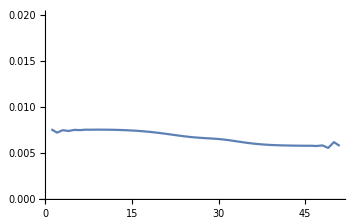

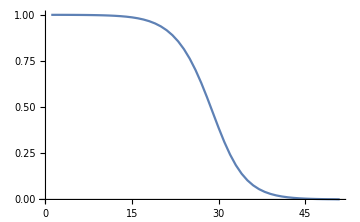

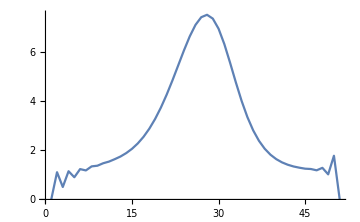

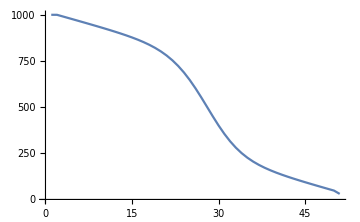

```mathematica
tplot= 100;
p1=ListPlot[ ρAll[[;;, tplot]], Joined-> True , PlotRange-> {Automatic, {0, 0.02}}, plotOptions]
p2=ListPlot[ ϕAll[[;;, tplot]], Joined-> True, PlotRange-> {Automatic, {0, 1}},plotOptions]
p3=ListPlot[ VAll[[;;, tplot]], Joined-> True, plotOptions]
p4=ListPlot[ cAll[[;;, tplot]], Joined-> True, plotOptions]
(*Show[p1,p2,p3, PlotRange-> All]*)
```

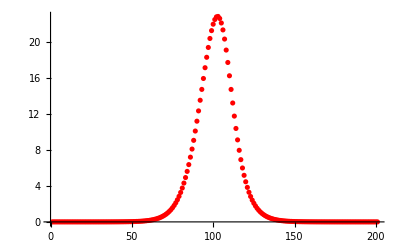

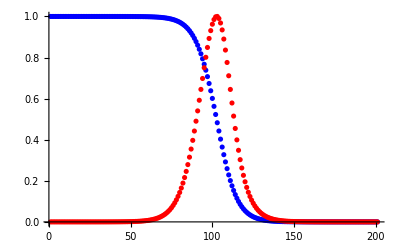

```mathematica
tplot= 5;
p1=ListPlot[ρAll[[;;,tplot]]/Max[ρAll[[;;,tplot]]], PlotStyle-> {Black} ];
p2=ListPlot[ϕAll[[;;,tplot]]/Max[ϕAll[[;;,tplot]]], PlotStyle-> {Blue} ];
p3=ListPlot[VAll[[;;,tplot]]/Max[VAll[[;;,tplot]]], PlotStyle-> {Red}, PlotRange->All ];
ListPlot[VAll[[;;,tplot]], PlotStyle-> {Red}, PlotRange->All ]
Show[ p2, p3, PlotRange-> All, AxesOrigin-> {0,0}]
```

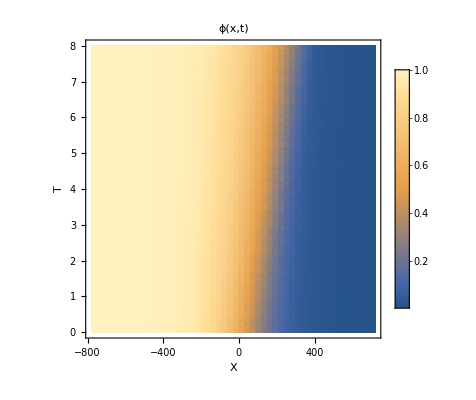

```mathematica
(* Zoom in *)
plotDataϕ=Flatten[Table[ {xmesh[[i]], tmesh[[j]], ϕAll[[i,j]]}, {i,Round[Nx/4],Round[Nx*3/4]}, {j,1, T+1}],1];pϕ=ListDensityPlot[plotDataϕ, PlotLabel-> "ϕ(x,t)", FrameLabel->{"X", "T"}, PlotLegends->Automatic ,PlotRange->All]
```

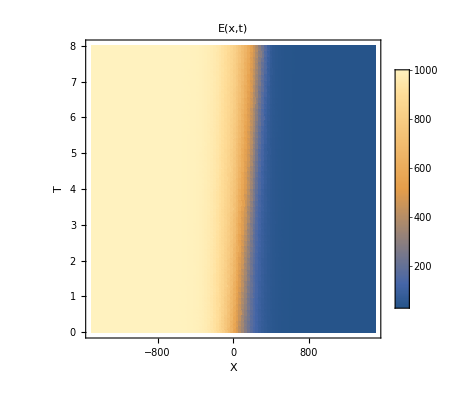

```mathematica
(*Stiffness *)
plotDataE=Flatten[Table[ {xmesh[[i]], tmesh[[j]],(eM(1-ϕAll[[i,j]])+eO ϕAll[[i,j]]) /. params}, {i,1, Nx+1}, {j,1, T+1}],1];ListDensityPlot[plotDataE, PlotLabel-> "E(x,t)", FrameLabel->{"X", "T"}, PlotLegends->Automatic ,PlotRange->All]
```

### Save data points for plots

```mathematica
OutNameRoot =FileNameJoin[{NotebookDirectory[], "Plots_model4b_FD_solver/", "simulation_set3/","data"}]
```

/Users/dang/Documents/Projects/Tabler_skull/Scripts/Scripts_mathematica/Plots_model4b_FD_solver/simulation_set3/data

```mathematica
(* Export parameters*)
(*AllParams=Join[ params, {"L"-> L, "tmax"-> tmax, "Nx"-> Nx, "T"-> T, "Dirichlet Boundaries"}]*)
allParams={eO,eM,η,ξ,τ,D1,α,ρdA,ρdB,ρh,aρ,a,"L","tmax","Nx","T"} ;
allValues=allParams /. params /. {"L"-> L, "tmax"-> tmax, "Nx"-> Nx, "T"-> T};
allParamsOut =Transpose[{allParams, allValues}]
Export[StringJoin[OutNameRoot, "_parameters.csv"], allParamsOut, "csv"]
```

{{eO,1000},{eM,30},{η,25/9},{ξ,0.28},{τ,10},{D1,15},{α,1/100000},{ρdA,0.0058},{ρdB,0.0076},{ρh,1/1000},{aρ,2},{a,6},{L,1500},{tmax,8},{Nx,100},{T,100}}

/Users/dang/Documents/Projects/Tabler_skull/Scripts/Scripts_mathematica/Plots_model4b_FD_solver/simulation_set3/data_parameters.csv

```mathematica
(*dataSave =Map[DecimalForm[#, dec]&, N[ρAll, dec], {2}];*)
Clear[dataSave];dataSave = N[ρAll]// TableForm;
Export[StringJoin[OutNameRoot, "_rho_1.csv"], dataSave, "CSV"]
Clear[dataSave];dataSave = N[ϕAll]// TableForm;
Export[StringJoin[OutNameRoot, "_phi_1.csv"], dataSave, "CSV"]
Clear[dataSave];dataSave =N[VAll] // TableForm;
Export[StringJoin[OutNameRoot, "_V_1.csv"], dataSave, "CSV"]
```

/Users/dang/Documents/Projects/Tabler_skull/Scripts/Scripts_mathematica/Plots_model4b_FD_solver/simulation_set3/data_rho_1.csv

/Users/dang/Documents/Projects/Tabler_skull/Scripts/Scripts_mathematica/Plots_model4b_FD_solver/simulation_set3/data_phi_1.csv

/Users/dang/Documents/Projects/Tabler_skull/Scripts/Scripts_mathematica/Plots_model4b_FD_solver/simulation_set3/data_V_1.csv

Save plots
Needs improvement...

```mathematica
fileOut =FileNameJoin[{NotebookDirectory[], "Plots_model4b_FD_solver/", "simulation_set3/","plot"}];
Export[StringJoin[fileOut, "_rho_1.eps"], pρ, "EPS"]
Export[StringJoin[fileOut, "_phi_1.eps"], pϕ, "EPS"]
Export[StringJoin[fileOut, "_V_1.eps"], pV, "EPS"]
(*Export[StringJoin[fileOut, "_200dpi.png"], pρ, "PNG", ImageResolution-> 200] ugly *)
```

/Users/dang/Documents/Projects/Tabler_skull/Scripts/Scripts_mathematica/Plots_model4b_FD_solver/simulation_set3/plot_rho_1.eps

/Users/dang/Documents/Projects/Tabler_skull/Scripts/Scripts_mathematica/Plots_model4b_FD_solver/simulation_set3/plot_phi_1.eps

/Users/dang/Documents/Projects/Tabler_skull/Scripts/Scripts_mathematica/Plots_model4b_FD_solver/simulation_set3/plot_V_1.eps

## Systematically calculate v for range of parameter values

### Calculate Δϕ

Numerically solve for wave velocity by shifting the profile ϕ[x, t] to ϕ[x + v δt, t + δt] and finding v for which the difference | ϕ[x, t] - ϕ[x + v δt, t + δt] | is minimized. 
Do for a range of values of t (denoted t1), but only one δt should be sufficient.

Boundaries: -L <= xp+vp δt <= L, so xp <= L - vp δt, so need to set this as integral / sum upper bound

```mathematica
(* quick calculation, without multiple T*)
(*
t1=20;
δt=10;
vpList=Range[0, 2*δt]/δt;
ΔϕFull=Sum@Table[
Sum[ (ϕAll[[x,t1 ]]-ϕAll[[x+vpList[[vj]] δt, t1+δt]] ), 
{x, 1, Nx-vpList[[vj]] δt}],
{vj, 1, Length[vpList]}
];
*)
```

```mathematica
T
```

100

```mathematica
Nx
```

100

```mathematica
(*Numerically test across a range of values for t and v*)
T1=20;δt=30;
t1All = Range[T1, T-δt, δt]; (* set time range*)
t1len= Length@t1All;
vpList=Range[0, 0.5*δt]/δt;
```

```mathematica
(*Test *)
(*(ϕAll[[x, t]]-ϕAll[[x+vp dt, t+dt]] )/.{x-> Nx/2, t-> T/2, vp-> vpList[[1]],dt -> 10}*)
```

Note: smallest possible difference in v testable is ΔxSet/δt, as the mesh size ΔxSet is fixed.
Testable difference in V (μm/hr):

```mathematica
N[ΔxSet/δt]
```

1.

```mathematica
Module[{dt = δt},
ΔϕFull=Abs[
Table[
Sum[ (ϕAll[[x, t1All[[tj]] ]]-ϕAll[[x+vpList[[vj]] dt, t1All[[tj]]+dt]] ), {x, 1, Nx-vpList[[vj]] dt}],
{tj, 1, t1len}, {vj, 1, Length[vpList]}
]
];
]
(*ΔϕFull=Table[  NIntegrate[Abs[((ϕsol/.{t->t1, x->xp})-(ϕsol/.{t->t1+δt, x->xp+vp δt} ) )] /.{x->xp} , {xp, -L, L-vp δt}, MaxRecursion->12],  {t1, t1All[[1]], t1All[[-1]], δt }, {vp, vpList[[1]], vpList[[-1]], δvp}];*)
```

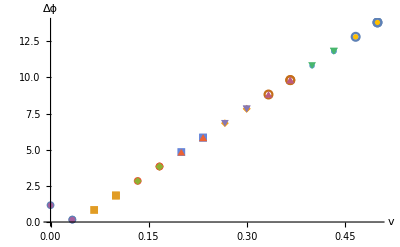

```mathematica
t1temp=ConstantArray[vpList, t1len] ;
plotdata=Partition[  Transpose[ {Flatten@t1temp, Flatten@ΔϕFull} ] , t1len];hplot=ListPlot[plotdata, Frame->False, PlotMarkers->{Automatic, 8},AxesLabel->{Style["v",Black, FontSize-> 20],Style["Δϕ", Black,FontSize-> 20] }, TicksStyle->Directive[Black,16]]
```

```mathematica
(* Save plot *)
fnameOut=StringJoin["/Users/dang/Documents/Projects/Tabler_skull/Scripts/Scripts_mathematica/Plots_model4b_FD_solver/simulation_set4_try_kD_profiles/","calculate_v_from_del_phi.eps"];
(*fnameOut=StringJoin[NotebookDirectory[] , "Velocity_data/", "del_phi_convergence_kF_", ToString[kF /. params],"_sM_30_sO_", ToString[sO /. params],"_epsphi_", ToString[ϵϕ],".eps"];*)
Export[fnameOut, hplot, "EPS"]
```

/Users/dang/Documents/Projects/Tabler_skull/Scripts/Scripts_mathematica/Plots_model4b_FD_solver/simulation_set4_try_kD_profiles/calculate_v_from_del_phi.eps

#### Find optimal v

```mathematica
(*Find minima of Δϕ for each t1*)
findmin=Position[#,Min[#]]&;
ϕminPos=Flatten[findmin/@ΔϕFull];
vValsϕmin = vpList[[ ϕminPos ]] (*values of velocity where the difference is minimal *)
```

{1/30,1/30}

```mathematica
(*Find minimal distance averaged over all t1*)
Δϕavg=Mean[ΔϕFull];
vInferred =vpList[[ Sequence@@First@findmin[Δϕavg] ]]  (* "optimal v" *)
```

1/30

```mathematica
ΔϕInferred= Δϕavg[[ Sequence@@First@findmin[Δϕavg] ]]
```

0.160242

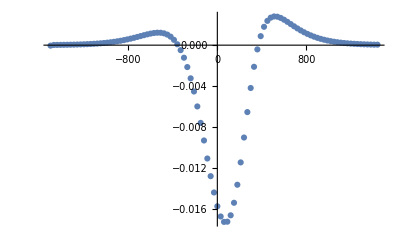

```mathematica
(* Plot difference between profiles given a certain shift *)
Module[{t1 = T1,dt = δt},
xvals = Table[xmesh[[xj]], {xj, 1, Nx-vInferred dt}];
δvals=Table[ϕAll[[x, t1 ]]-ϕAll[[x+vInferred dt, t1+dt]], {x, 1, Nx-vInferred dt}];
]
p1=ListPlot[Transpose[{xvals, δvals}],PlotRange-> All,PlotLegends->"Δϕ"]
```

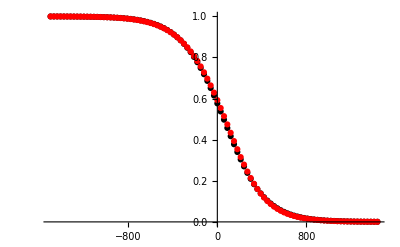

```mathematica
(* Plot both profiles given a certain shift *)
Module[{t1 = T1,dt = δt},
xvals = Table[xmesh[[xj]], {xj, 1, Nx-vInferred dt}];
ϕ1vals=Table[ϕAll[[x, t1 ]], {x, 1, Nx-vInferred dt}];
ϕ2vals=Table[ϕAll[[x+vInferred dt, t1+dt]], {x, 1, Nx-vInferred dt}];
]

p1=ListPlot[Transpose[{xvals, ϕ1vals}],PlotRange-> All,PlotLegends->"ϕ1", PlotStyle-> {Black}];
p2=ListPlot[Transpose[{xvals, ϕ2vals}],PlotRange-> All,PlotLegends->"ϕ2", PlotStyle-> {Red}];
Show[p1,p2]
```

In units of μm/hr:

```mathematica
N[vInferred*ΔxSet/ΔtSet]
```

12.5

### Width of ϕ profile

Obtain by simply setting thresholds ϕ_L≤ ϕ ≤ ϕ_H

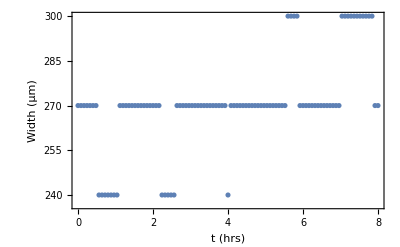

```mathematica
ϕL=0.2; ϕH=0.8;
ϕMid=Boole@Map[(ϕL<#)&& (#<ϕH)&,ϕAll, {2}];
AllWidths=Total[ϕMid]*ΔxSet;

ϕwidth = Mean[ AllWidths[[Round[T/2];;]] ];
ListPlot[ Transpose[{tmesh,AllWidths}] , Frame-> True, FrameLabel->{"t (hrs)", "Width (μm)"}]
```

```mathematica
N[ϕwidth]
```

278.077

### Organize data together and save

Save parameters + inferred v + error Δϕ

```mathematica
params
```

{eO→1000,eM→30,ηM→5/18,ηO→250/9,ξ→2/9,τ→10,D1→15,α→1/100000,ρdA→0.0058,ρdB→0.0076,aρ→8,a→8,ρh→1/1000,f→0}

```mathematica
(*vars={{τ,ρdA,ρdB,ρh},{D1,α,kF},{fc,ξ,χ,η,κ},{sM,sO,a,τs}};*)
vars = {eO,eM,η,ξ,τ,D1,α,ρdA,ρdB,aρ,a,ρh};
varsVals=Map[Replace[#, Flatten@params]&,vars, 2]
```

{1000,30,ηM (1-ϕ[x,t])+ηO ϕ[x,t],2/9,10,15,1/100000,0.0058,0.0076,8,8,1/1000}

deltavUnits:

```mathematica
(*varsOut=ToString/@{{tau,rhoA,rhoB,rhoh},{D1,alpha,kDiff},{fc,xi,chi,eta,kappa},{sM,sO,a,taus},{"xmin", "xmax", "tmax", "deltat", "deltavp"},{"vInferred", "DeltaphiInferred"}}*)
varsOut=ToString/@{{eO,eM,eta,xi,tau,D1,alpha,rhodA,rhodB,aRho,a,rhoh},{"xmin", "xmax", "tmax", "deltat", "deltavUnits"},{"vInferred", "DeltaphiInferred", "vInferredMicrons", "phiWidthMicrons"}}
varsValsOut=N/@Join[varsVals,{{-L,L,tmax,δt,ΔxSet/δt}},{{vInferred, ΔϕInferred, vInferred*ΔxSet/ΔtSet, ϕwidth}}]
```

{{eO, eM, eta, xi, tau, D1, alpha, rhodA, rhodB, aRho, a, rhoh},{xmin, xmax, tmax, deltat, deltavUnits},{vInferred, DeltaphiInferred, vInferredMicrons, phiWidthMicrons}}

{1000.,30.,ηM (1.-1. ϕ[x,t])+ηO ϕ[x,t],0.222222,10.,15.,0.00001,0.0058,0.0076,8.,8.,0.001,{-1500.,1500.,8.,30.,1.},{0.0333333,0.398626,12.5,278.077}}

```mathematica
(*fnameOut=StringJoin[NotebookDirectory[] , "Velocity_data/", "vdata_kF_", ToString[kF /. params],"_sM_30_sO", ToString[sO /. params],"_es_", ToString[ϵs],"_epsphi_", ToString[ϵϕ],"_t20.csv"]*)
fnameOut=StringJoin["/Users/dang/Documents/Projects/Tabler_skull/Scripts/Scripts_mathematica/Plots_model4b_FD_solver/", "simulation_set3/", "velocity_data.csv"] 
(*Export[fnameOut, {varsOut,varsValsOut}, "CSV"]*)
```

/Users/dang/Documents/Projects/Tabler_skull/Scripts/Scripts_mathematica/Plots_model4b_FD_solver/simulation_set3/velocity_data.csv

/Users/dang/Documents/Projects/Tabler_skull/Scripts/Scripts_mathematica/Plots_model4b_FD_solver/simulation_set3/velocity_data.csv

## Compare multiple simulations

#### Load data

```mathematica
(* Load data*)
LoadFolder = "/Users/dang/Documents/Projects/Tabler_skull/Scripts/Scripts_mathematica/Plots_model4b_FD_solver/simulation_set4_try_kD_profiles/0_constant/data";
ρAll0=Import[StringJoin[LoadFolder, "_rho_1.csv"]];
ϕAll0=Import[StringJoin[LoadFolder, "_phi_1.csv"]];
VAll0=Import[StringJoin[LoadFolder, "_V_1.csv"]];
params0 = Import[StringJoin[LoadFolder, "_parameters.csv"]];

(* Load data*)
LoadFolder = "/Users/dang/Documents/Projects/Tabler_skull/Scripts/Scripts_mathematica/Plots_model4b_FD_solver/simulation_set4_try_kD_profiles/1_linear/data";
ρAll1=Import[StringJoin[LoadFolder, "_rho_1.csv"]];
ϕAll1=Import[StringJoin[LoadFolder, "_phi_1.csv"]];
VAll1=Import[StringJoin[LoadFolder, "_V_1.csv"]];
params1 = Import[StringJoin[LoadFolder, "_parameters.csv"]];

(* Load data*)
LoadFolder = "/Users/dang/Documents/Projects/Tabler_skull/Scripts/Scripts_mathematica/Plots_model4b_FD_solver/simulation_set4_try_kD_profiles/2_sigmoidal/data";
ρAll2=Import[StringJoin[LoadFolder, "_rho_1.csv"]];
ϕAll2=Import[StringJoin[LoadFolder, "_phi_1.csv"]];
VAll2=Import[StringJoin[LoadFolder, "_V_1.csv"]];
params2 = Import[StringJoin[LoadFolder, "_parameters.csv"]];

(* Load data*)
LoadFolder = "/Users/dang/Documents/Projects/Tabler_skull/Scripts/Scripts_mathematica/Plots_model4b_FD_solver/simulation_set4_try_kD_profiles/3_gaussian/data";
ρAll3=Import[StringJoin[LoadFolder, "_rho_1.csv"]];
ϕAll3=Import[StringJoin[LoadFolder, "_phi_1.csv"]];
VAll3=Import[StringJoin[LoadFolder, "_V_1.csv"]];
params3 = Import[StringJoin[LoadFolder, "_parameters.csv"]];

(* Load data*)
LoadFolder = "/Users/dang/Documents/Projects/Tabler_skull/Scripts/Scripts_mathematica/Plots_model4b_FD_solver/simulation_set4_try_kD_profiles/3b_gaussian_shifted_left/data";
ρAll3b=Import[StringJoin[LoadFolder, "_rho_1.csv"]];
ϕAll3b=Import[StringJoin[LoadFolder, "_phi_1.csv"]];
VAll3b=Import[StringJoin[LoadFolder, "_V_1.csv"]];
params3b = Import[StringJoin[LoadFolder, "_parameters.csv"]];

(* Load data*)
LoadFolder = "/Users/dang/Documents/Projects/Tabler_skull/Scripts/Scripts_mathematica/Plots_model4b_FD_solver/simulation_set4_try_kD_profiles/3c_gaussian_shifted_right/data";
ρAll3c=Import[StringJoin[LoadFolder, "_rho_1.csv"]];
ϕAll3c=Import[StringJoin[LoadFolder, "_phi_1.csv"]];
VAll3c=Import[StringJoin[LoadFolder, "_V_1.csv"]];
params3c = Import[StringJoin[LoadFolder, "_parameters.csv"]];
```

Common parameters

```mathematica
(*params={eO-> 1000, eM-> 30, η-> 25/9, ξ-> 5/18, τ-> 10, D1->1000, α-> 1/1000, ρdA-> 5.8*10^(-3), ρdB->7.6*10^(-3), ρh->1*10^(-3), aρ-> 8,a->8}; *)
L=1500;
tmax=8;
Nx = 100;
T=100;
```

```mathematica
(* Define mesh *)
ΔxSet = 2L/(Nx);
ΔtSet = tmax/T;
xmesh= Range[-L, L, ΔxSet];
tmesh =Range[0, tmax, tmax/T];
```

#### Plot results

```mathematica
plotOptions = {ImageSize-> Small,PerformanceGoal-> "Quality",PlotLegends->Automatic,PlotRange->All, PlotLegends->Placed[BarLegend[Automatic],Right],ImageSize->Small,TicksStyle->Large,LabelStyle->{FontFamily->"Arial",FontSize->14,GrayLevel[0]},AspectRatio->Full}
```

{ImageSize→Small,PerformanceGoal→Quality,PlotLegends→Automatic,PlotRange→All,PlotLegends→Placed[BarLegend[Automatic],Right],ImageSize→Small,TicksStyle→Large,LabelStyle→{FontFamily→Arial,FontSize→14,GrayLevel[0]},AspectRatio→Full}

```mathematica
plotDataϕ0=Flatten[Table[ {xmesh[[i]],tmesh[[j]],ϕAll0[[i,j]]}, {i,1,Nx+1}, {j,1,T+1}],1];
pϕ0=ListDensityPlot[plotDataϕ0, PlotLabel-> "ϕ(x,t)", FrameLabel->{"X", "T"}, plotOptions];
plotDataϕ1=Flatten[Table[ {xmesh[[i]],tmesh[[j]],ϕAll1[[i,j]]}, {i,1,Nx+1}, {j,1,T+1}],1];
pϕ1=ListDensityPlot[plotDataϕ1, PlotLabel-> "ϕ(x,t)", FrameLabel->{"X", "T"}, plotOptions];
plotDataϕ2=Flatten[Table[ {xmesh[[i]],tmesh[[j]],ϕAll2[[i,j]]}, {i,1,Nx+1}, {j,1,T+1}],1];
pϕ2=ListDensityPlot[plotDataϕ2, PlotLabel-> "ϕ(x,t)", FrameLabel->{"X", "T"}, plotOptions];
plotDataϕ3=Flatten[Table[ {xmesh[[i]],tmesh[[j]],ϕAll3[[i,j]]}, {i,1,Nx+1}, {j,1,T+1}],1];
pϕ3=ListDensityPlot[plotDataϕ3, PlotLabel-> "ϕ(x,t)", FrameLabel->{"X", "T"}, plotOptions];
plotDataϕ3b=Flatten[Table[ {xmesh[[i]],tmesh[[j]],ϕAll3b[[i,j]]}, {i,1,Nx+1}, {j,1,T+1}],1];
pϕ3b=ListDensityPlot[plotDataϕ3, PlotLabel-> "ϕ(x,t)", FrameLabel->{"X", "T"}, plotOptions];
plotDataϕ3c=Flatten[Table[ {xmesh[[i]],tmesh[[j]],ϕAll3c[[i,j]]}, {i,1,Nx+1}, {j,1,T+1}],1];
pϕ3c=ListDensityPlot[plotDataϕ3, PlotLabel-> "ϕ(x,t)", FrameLabel->{"X", "T"}, plotOptions];
AllPlots=GraphicsRow[{pϕ0, pϕ1,pϕ2, pϕ3},ImageSize->Full,ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}} ]
AllPlots=GraphicsRow[{pϕ3, pϕ3b, pϕ3c},ImageSize->Full,ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}} ]
```

-Graphics-

-Graphics-

#### Plot profiles at fixed time

```mathematica
plotOptions = {ImageSize-> Medium,PerformanceGoal-> "Quality",PlotLegends->Automatic,PlotRange->All,TicksStyle->Large,LabelStyle->{FontFamily->"Arial",FontSize->10,GrayLevel[0]}}
```

{ImageSize→Medium,PerformanceGoal→Quality,PlotLegends→Automatic,PlotRange→All,TicksStyle→Large,LabelStyle→{FontFamily→Arial,FontSize→10,GrayLevel[0]}}

```mathematica
tplot= T;
pρ0=ListPlot[Transpose[{xmesh,ρAll0[[;;, tplot]]}], Joined-> True, plotOptions, PlotStyle->{Blue, Opacity[0.5]}];
pϕ0=ListPlot[Transpose[{xmesh,ϕAll0[[;;, tplot]]}], Joined-> True,plotOptions, PlotStyle->{Blue, Opacity[0.5]}];
pV0=ListPlot[Transpose[{xmesh,VAll0[[;;, tplot]] }], Joined-> True, plotOptions, PlotStyle->{Blue, Opacity[0.5]}];

pρ1=ListPlot[Transpose[{xmesh,ρAll1[[;;, tplot]]}], Joined-> True, plotOptions, PlotStyle->{Blue, Opacity[0.5]}];
pϕ1=ListPlot[Transpose[{xmesh,ϕAll1[[;;, tplot]]}], Joined-> True,plotOptions, PlotStyle->{Blue, Opacity[0.5]}];
pV1=ListPlot[Transpose[{xmesh,VAll1[[;;, tplot]] }], Joined-> True, plotOptions, PlotStyle->{Blue, Opacity[0.5]}];

pρ2=ListPlot[Transpose[{xmesh, ρAll2[[;;, tplot]]}], Joined-> True,  plotOptions, PlotStyle->{Red, Opacity[0.5]}];
pϕ2=ListPlot[ Transpose[{xmesh,ϕAll2[[;;, tplot]]}], Joined-> True, plotOptions, PlotStyle->{Red, Opacity[0.5]}];
pV2=ListPlot[ Transpose[{xmesh,VAll2[[;;, tplot]]}], Joined-> True, plotOptions, PlotStyle->{Red, Opacity[0.5]}];

pρ3=ListPlot[ Transpose[{xmesh,ρAll3[[;;, tplot]]}], Joined-> True,  plotOptions, PlotStyle->{Black, Opacity[0.5]}];
pϕ3=ListPlot[ Transpose[{xmesh,ϕAll3[[;;, tplot]]}], Joined-> True, plotOptions, PlotStyle->{Black, Opacity[0.5]}];
pV3=ListPlot[ Transpose[{xmesh,VAll3[[;;, tplot]]}], Joined-> True, plotOptions, PlotStyle->{Black, Opacity[0.5]}];

pρ3b=ListPlot[ Transpose[{xmesh,ρAll3b[[;;, tplot]]}], Joined-> True,  plotOptions, PlotStyle->{Red, Opacity[0.5]}];
pϕ3b=ListPlot[ Transpose[{xmesh,ϕAll3b[[;;, tplot]]}], Joined-> True, plotOptions, PlotStyle->{Red, Opacity[0.5]}];
pV3b=ListPlot[ Transpose[{xmesh,VAll3b[[;;, tplot]]}], Joined-> True, plotOptions, PlotStyle->{Red, Opacity[0.5]}];

pρ3c=ListPlot[ Transpose[{xmesh,ρAll3c[[;;, tplot]]}], Joined-> True,  plotOptions, PlotStyle->{Green, Opacity[0.5]}];
pϕ3c=ListPlot[ Transpose[{xmesh,ϕAll3c[[;;, tplot]]}], Joined-> True, plotOptions, PlotStyle->{Green, Opacity[0.5]}];
pV3c=ListPlot[ Transpose[{xmesh,VAll3c[[;;, tplot]]}], Joined-> True, plotOptions, PlotStyle->{Green, Opacity[0.5]}];
```

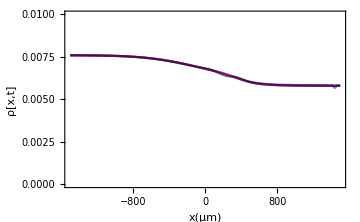

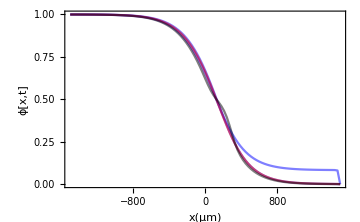

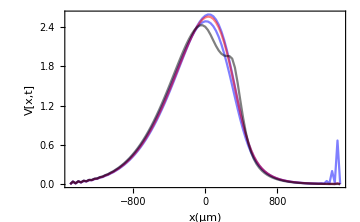

```mathematica
Show[pρ0, pρ1,pρ2,pρ3,PlotRange->{Automatic, {0, 0.01}}, AxesOrigin-> {0,0}, Frame-> True, FrameLabel->{"x(μm)", "ρ[x,t]"}]
Show[pϕ0, pϕ1,pϕ2,pϕ3,PlotRange-> All, Frame-> True, FrameLabel->{"x(μm)", "ϕ[x,t]"}]
Show[pV0, pV1,pV2,pV3,PlotRange-> All, Frame-> True, FrameLabel->{"x(μm)", "V[x,t]"}]
```

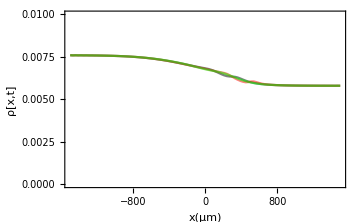

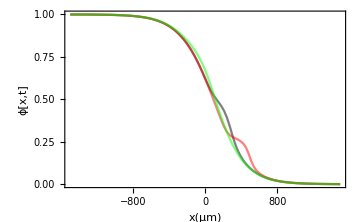

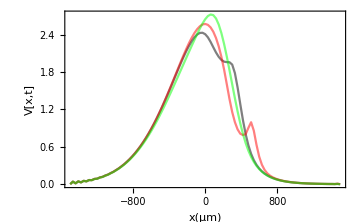

```mathematica
Show[pρ3,pρ3b,pρ3c,PlotRange->{Automatic, {0, 0.01}}, AxesOrigin-> {0,0}, Frame-> True, FrameLabel->{"x(μm)", "ρ[x,t]"}]
Show[pϕ3,pϕ3b,pϕ3c,PlotRange-> All, Frame-> True, FrameLabel->{"x(μm)", "ϕ[x,t]"}]
Show[pV3,pV3b,pV3c,PlotRange-> All, Frame-> True, FrameLabel->{"x(μm)", "V[x,t]"}]
```

#### Plot difference between profiles

```mathematica
pρ21=ListPlot[Transpose[{xmesh, ρAll2[[;;, tplot]]-ρAll1[[;;, tplot]]}], Joined-> True, plotOptions, PlotStyle->{Purple, Opacity[0.5]}];
pρ31=ListPlot[Transpose[{xmesh, ρAll3[[;;, tplot]]-ρAll1[[;;, tplot]]}], Joined-> True, plotOptions, PlotStyle->{Black, Opacity[0.5]}];
pρ32=ListPlot[Transpose[{xmesh, ρAll3[[;;, tplot]]-ρAll2[[;;, tplot]]}], Joined-> True, plotOptions, PlotStyle->{Orange, Opacity[0.5]}];
ϕρ21=ListPlot[Transpose[{xmesh, ϕAll2[[;;, tplot]]-ϕAll1[[;;, tplot]]}], Joined-> True, plotOptions, PlotStyle->{Purple, Opacity[0.5]}];
ϕρ31=ListPlot[Transpose[{xmesh, ϕAll3[[;;, tplot]]-ϕAll1[[;;, tplot]]}], Joined-> True, plotOptions, PlotStyle->{Black, Opacity[0.5]}];
ϕρ32=ListPlot[Transpose[{xmesh, ϕAll3[[;;, tplot]]-ϕAll2[[;;, tplot]]}], Joined-> True, plotOptions, PlotStyle->{Orange, Opacity[0.5]}];
Vρ21=ListPlot[Transpose[{xmesh, VAll2[[;;, tplot]]-VAll1[[;;, tplot]]}], Joined-> True, plotOptions, PlotStyle->{Purple, Opacity[0.5]}];
Vρ31=ListPlot[Transpose[{xmesh, VAll3[[;;, tplot]]-VAll1[[;;, tplot]]}], Joined-> True, plotOptions, PlotStyle->{Black, Opacity[0.5]}];
Vρ32=ListPlot[Transpose[{xmesh, VAll3[[;;, tplot]]-VAll2[[;;, tplot]]}], Joined-> True, plotOptions, PlotStyle->{Orange, Opacity[0.5]}];
```

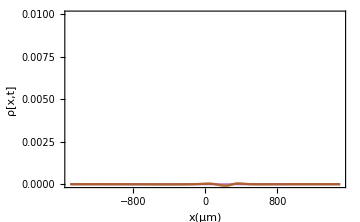

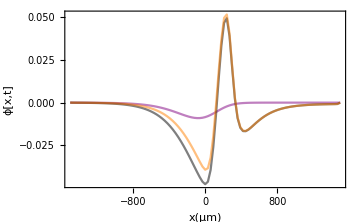

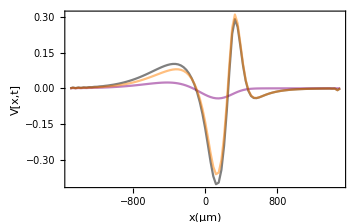

```mathematica
Show[pρ21,pρ31,pρ32,PlotRange->{Automatic, {0, 0.01}}, AxesOrigin-> {0,0}, Frame-> True, FrameLabel->{"x(μm)", "ρ[x,t]"}]
Show[ϕρ21,ϕρ31,ϕρ32, PlotRange-> All, Frame-> True, FrameLabel->{"x(μm)", "ϕ[x,t]"}]
Show[Vρ21,Vρ31,Vρ32, PlotRange-> All, Frame-> True, FrameLabel->{"x(μm)", "V[x,t]"}]
```

## Parameters and velocities

List of parameters and velocities.

```mathematica
(*Set 2a*)
params={eO-> 1000, eM-> 30, η-> 25/9, ξ-> 3/18, τ-> 10, D1->15, α-> 4*10^(-5), ρdA-> 5.8*10^(-3), ρdB->7.6*10^(-3), aρ->4,a->4,ρh->1*10^(-3)};
L=1500;
tmax=8;
vOut = 25;
```

```mathematica
(*Set 2b*)
params={eO-> 1000, eM-> 30, η-> 25/9, ξ-> 3/18, τ-> 10, D1->15, α-> 1*10^(-5), ρdA-> 5.8*10^(-3), ρdB->7.6*10^(-3), aρ->4,a->4,ρh->1*10^(-3)};
L=1500;
tmax=8;
vOut = 12.5;
```

```mathematica
(* set 4 *)
params={eO-> 1000, eM-> 30, η-> 25/9, ξ-> 5/18, τ-> 10, D1->15, α-> 2*10^(-5), ρdA-> 5.8*10^(-3), ρdB->7.6*10^(-3),aρ->4,a->4,ρh->5*10^(-3)};
L=1500;
tmax=8;
kD1:=α (e-eM);
kD2:=α eO  Tanh[(e-eM)/eO] /. params;
kD3:=0.02*Exp[-(e-(eO-eM)/2)^2/(2*((eO-eM)/8)^2)]
kD:=kD1
```

Part::partw: Part 16 of {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} does not exist.

Part::partw: Part 17 of {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} does not exist.

Part::partw: Part 18 of {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-